```mathematica
PhasePlot[f_,ic_,ti_,opts___]:=Block[{i,n=Length[ic],ff,ivp,sol,t1,t2,tmin,tmax,phaseplot,ps,pvf,vf,vfr,pev,a,ev,evs,optss},
ff=f /. {x->x[t],y->y[t]};
If[Head[ti]===List,{tmin,tmax}=ti,{tmin,tmax}={-ti,ti}];
pfv=VectorField /. {opts,VectorField->False};
pev=EigenVectors /. {opts,EigenVectors->False};
ps=PlotStyle /.{opts,PlotStyle->{}};
optss=DeleteCases[{opts},VectorField->_];
optss=DeleteCases[optss,EigenVectors->_];
optss=DeleteCases[optss,PlotStyle->_];
optss[[0]]=Sequence;
vf=Graphics[];
ev=Graphics[];
vfr=PlotRange /. {opts, PlotRange->{{-1,1},{-1,1}}};
If[pfv,vf=VectorPlot[f,{x,vfr[[1,1]],vfr[[1,2]]},{y,vfr[[2,1]],vfr[[2,2]]},Frame->False,Axes->True,Ticks->False,VectorPoints->8,VectorScale->{0.1,0.3}]];
If[pev,
a=Transpose[{f/. {x->1,y->0},f/. {x->0,y->1}}];
evs=Eigensystem[a][[2]];
If[Im[evs]=={{0,0},{0,0}},
ev=ParametricPlot[evs t,{t,-100,100},PlotStyle->{Red,Red}]];
];
Off[NDSolve::"ndsz"];
Do[
ivp={x'[t]==ff[[1]],y'[t]==ff[[2]],x[0]==ic[[i,1]],y[0]==ic[[i,2]]};
sol=NDSolve[ivp,{x[t],y[t]},{t,tmin,tmax}];
{t1,t2}=sol[[1]][[1]][[2]][[0]][[1]][[1]];
phaseplot[i]=ParametricPlot[{x[t],y[t]} /. sol,{t,t1,t2},PlotStyle->ps]
,{i,1,n}];
On[NDSolve::"ndsz"];
Show[Table[phaseplot[i],{i,1,n}],vf,ev,optss]
];
```

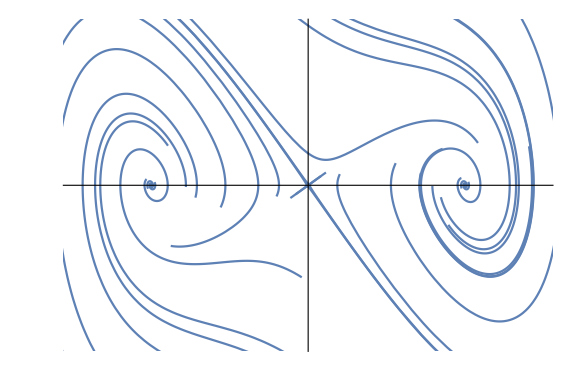

```mathematica
duffing07 = PhasePlot[{y,-0.7*y+x-x^3},{
{0,0.2},{0,1},{-1,0.2},{-1,1},{1,0.2},{1,1},{0,2},{1,-2},{1,2},{-1,-2},{-1,2},{0,-2},{0,1.2},{0,-1.25},{0,1.5},{0,-1.5},
{1,-0.01},{1,0.01},{-1,-0.01},{-1,0.01},
{0,-0.01},{0,0.01},{-0.01,0},{0.01,0}
},4,ImageSize->Large,PlotRange->{{-1.5,1.5},{-1,1}},Ticks->False]
```

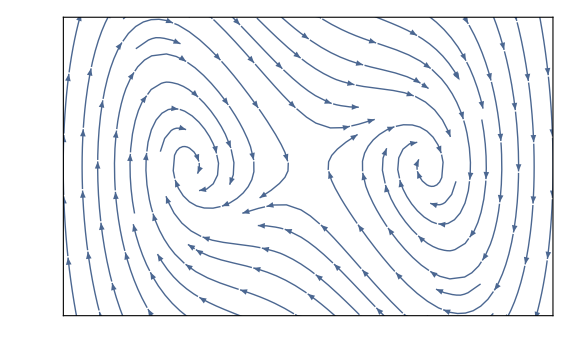

```mathematica
duffing07Vec=StreamPlot[{y, -0.7*y+x-x^3},{x,-3,3},{y,-3,3},
ImageSize->Large,AspectRatio->Automatic,FrameTicks->None,StreamPoints->Fine,PlotRange->{{-2,2},{-1.2,1.2}}]
```

```mathematica
Export["duffing07Vec.pdf",duffing07Vec]
```

duffing07Vec.pdf

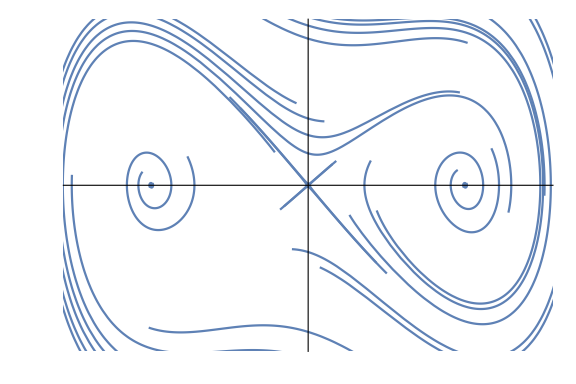

```mathematica
duffing03 = PhasePlot[{y,-0.3*y+x-x^3},{
{0,0.2},{0,1},{-1,0.2},{-1,1},{1,0.2},{1,1},{0,2},{1,-2},{1,2},{-1,-2},{-1,2},{0,-2},{0,1.2},{0,-1.25},{0,1.5},{0,-1.5},
{1,-0.01},{1,0.01},{-1,-0.01},{-1,0.01},
{0,-0.01},{0,0.01},{-0.01,0},{0.01,0}
},4,ImageSize->Large,PlotRange->{{-1.5,1.5},{-1,1}},Ticks->False]
```

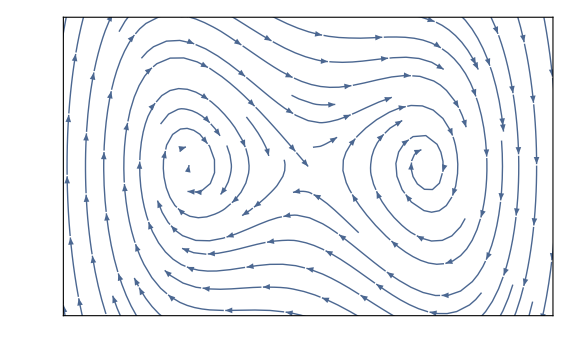

```mathematica
duffing03Vec=StreamPlot[{y, -0.3*y+x-x^3},{x,-3,3},{y,-3,3},
ImageSize->Large,AspectRatio->Automatic,FrameTicks->None,StreamPoints->Fine,PlotRange->{{-2,2},{-1.2,1.2}}]
```

```mathematica
Export["duffing03Vec.pdf",duffing03Vec]
```

duffing03Vec.pdf

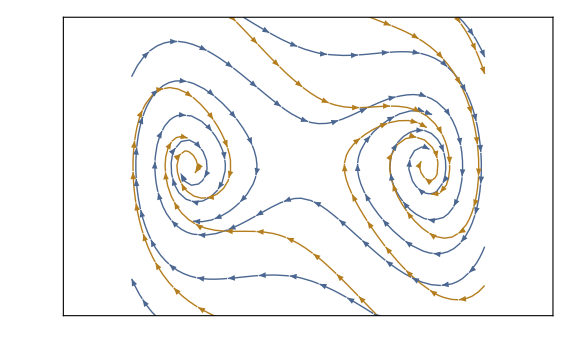

```mathematica
duffing0307Vec=StreamPlot[{{y, -0.3*y+x-x^3},{y, -0.7*y+x-x^3}},{x,-1.5,1.5},{y,-3,3},
ImageSize->Large,AspectRatio->Automatic,FrameTicks->None,PlotRange->{{-2,2},{-1.2,1.2}},StreamPoints->10]
```

```mathematica
Export["duffing0307Vec.pdf",duffing0307Vec]
```

duffing0307Vec.pdf

```mathematica
undampedDuffing = StreamPlot[{y,x-x^3},{x,-1.5,1.5},{y,-1,1},ImageSize->Large,FrameTicks->None,AspectRatio->Automatic,PlotRange->{{-1.5,1.5},{-1,1}},StreamPoints->20]
```